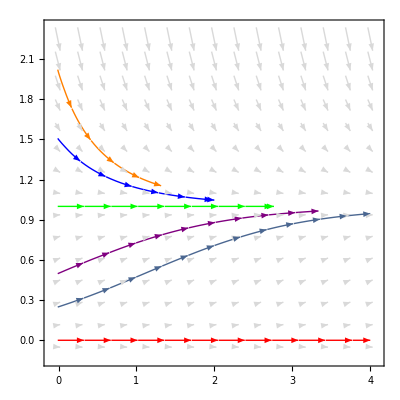

```mathematica
a=1;L=1;M=1;
VectorPlot[{1,L*a*x-M*x^2},{t,-0.01,4},{x,-0.05,2.25},VectorScale->{Tiny},VectorStyle->LightGray,StreamStyle->Thin,
StreamPoints->{{{{0,0},Red},{{0,0.25},Automatic},{{0,0.5},Purple},{{0,1},Green},{{0,1.5},Blue},{{0,2},Orange}}}]
```

```mathematica
Solve[N(r-a(N-b)^2)==0,N]
```

```mathematica
{{N->0},{N->(√a b-√r)/(√a)},{N->(√a b+√r)/(√a)}}
```

```mathematica
D[N(r-a(N-b)^2),N]
```

3-(-1+N)^2-2 (-1+N) N

```mathematica
Simplify[3-(-1+N)^2-2 (-1+N) N]
```

2+4 N-3 N^2

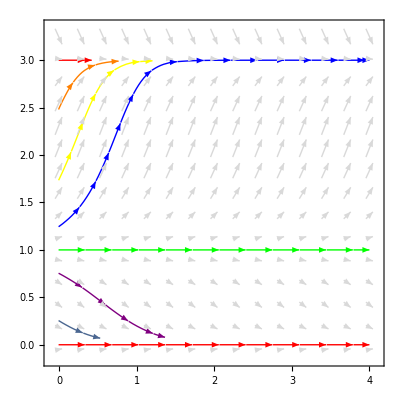

```mathematica
a=1;r=1;b=2;
VectorPlot[{1,n(r-a(n-b)^2)},{t,-0.01,4},{n,-0.05,3.25},VectorStyle->LightGray,VectorScale->{Tiny},StreamStyle->Thin,
StreamPoints->{{{{0,0},Red},{{0,0.25},Automatic},{{0,0.75},Purple},{{0,1},Green},{{0,1.25},Blue},{{0,1.75},Yellow},{{0,2.5},Orange},{{0,3},Red}}}]
```

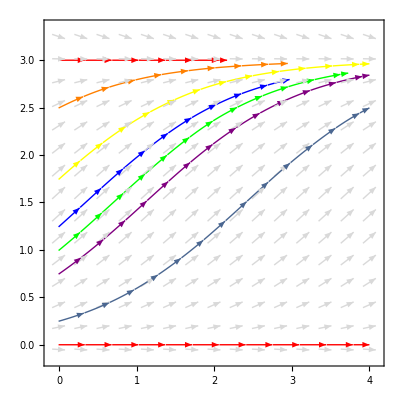
{-Graphics-,-Graphics-}

```mathematica
a=1;r=1;b=2;k=3;
{VectorPlot[{1,n(r-a(n-b)^2)},{t,-0.01,4},{n,-0.05,3.25},VectorStyle->LightGray,VectorScale->{Tiny},StreamStyle->Thin,
StreamPoints->{{{{0,0},Red},{{0,0.25},Automatic},{{0,0.75},Purple},{{0,1},Green},{{0,1.25},Blue},{{0,1.75},Yellow},{{0,2.5},Orange},{{0,3},Red}}}],VectorPlot[{1,r*n(1-n/k)},{t,-0.01,4},{n,-0.05,3.25},VectorStyle->LightGray,VectorScale->{Tiny},StreamStyle->Thin,
StreamPoints->{{{{0,0},Red},{{0,0.25},Automatic},{{0,0.75},Purple},{{0,1},Green},{{0,1.25},Blue},{{0,1.75},Yellow},{{0,2.5},Orange},{{0,3},Red}}}]}
```

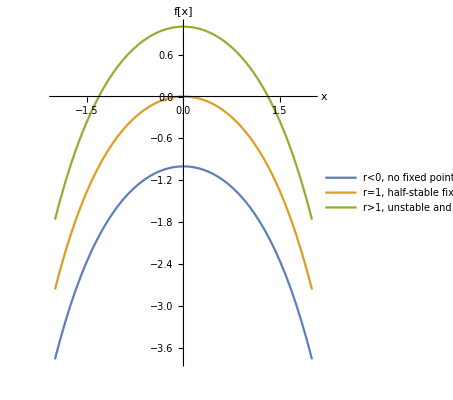
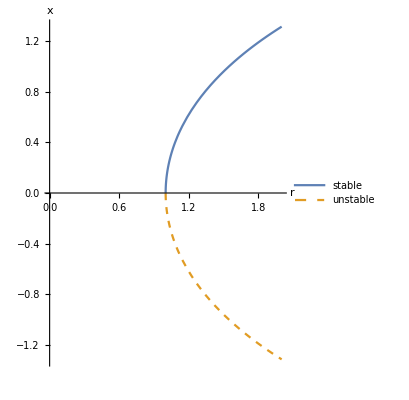

```mathematica
f[r_]:=r-Cosh[x];
{Plot[{f[0],f[1],f[2]},{x,-2,2},AxesLabel->{"x","f[x]"},PlotLegends->Placed[{"r<0, no fixed points","r=1, half-stable fixed point","r>1, unstable and stable fixed points"},Below],AspectRatio->Automatic],Plot[{ArcCosh[r],-ArcCosh[r]},{r,0,2},AxesLabel->{"r","x"},PlotStyle->{Thick, Dashed},PlotLegends->Placed[{"stable","unstable"},Below],AspectRatio->Automatic]}
```

```mathematica
f[x_]:=x/2-x/(x+1);
Solve[D[f[x],x]==0,x]
Simplify[{f[-1-√2],f[-1+√2]}]
```

{{x→-1-√2},{x→-1+√2}}

{-3/2-√2,-3/2+√2}

```mathematica
Solve[r+x/2-x/(x+1)==0,x]
```

{{x→1/2 (1-2 r-√(1-12 r+4 r^2))},{x→1/2 (1-2 r+√(1-12 r+4 r^2))}}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

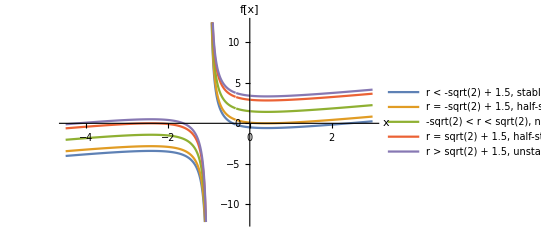
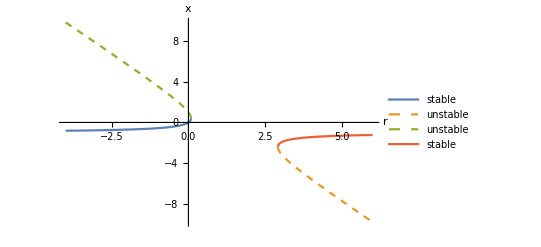

```mathematica
f[r_]:=r+x/2-x/(x+1);
{Plot[{f[-.5],f[-√2+1.5],f[1.5],f[√2+1.5],f[√2+2]},{x,-4.5,3},Exclusions->1/f[x]==0,AxesLabel->{"x","f[x]"},PlotLegends->Placed[{"r < -sqrt(2) + 1.5, stable and unstable fixed points", "r = -sqrt(2) + 1.5, half-stable fixed point", "-sqrt(2) < r < sqrt(2), no fixed point", "r = sqrt(2) + 1.5, half-stable fixed point", "r > sqrt(2) + 1.5, unstable and stable fixed points"},Below]], Plot[{Piecewise[{{1/2 (1-2 r-√(1-12 r+4 r^2)),r<1},{Infinity,r>1}}],Piecewise[{{1/2 (1-2 r-√(1-12 r+4 r^2)),r>1},{Infinity,r<1}}],Piecewise[{{1/2 (1-2 r+√(1-12 r+4 r^2)),r<1},{Infinity,r>1}}],Piecewise[{{1/2 (1-2 r+√(1-12 r+4 r^2)),r>1},{Infinity,r<1}}]},{r,-4,6},AxesLabel->{"r","x"},PlotLegends->Placed[{"stable","unstable","unstable","stable"},Below],PlotStyle->{Thick,Dashed,Dashed,Thick}]}
```

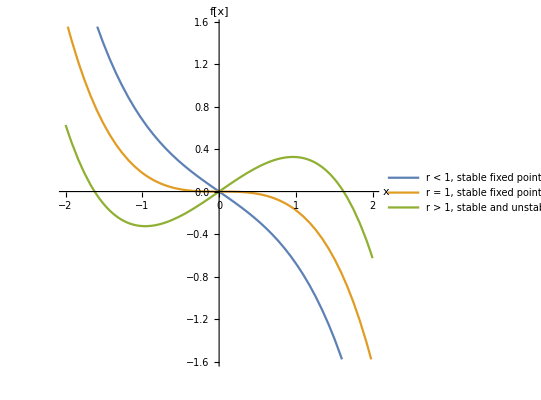
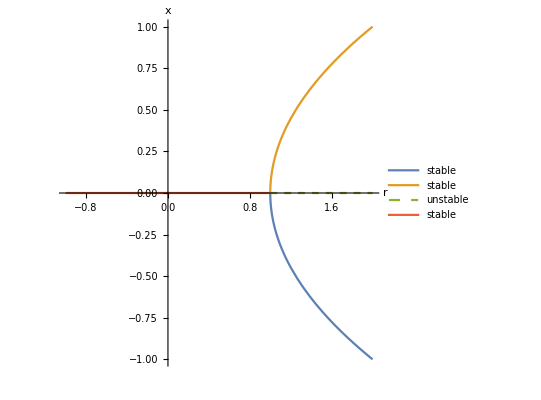

```mathematica
f[r_]:=r*x-Sinh[x];
{Plot[{f[0.5],f[1],f[1.5]},{x,-2,2},PlotLegends->Placed[{"r < 1, stable fixed point", "r = 1, stable fixed point", "r > 1, stable and unstable and stable fixed points"},Below],AxesLabel->{"x","f[x]"},AspectRatio->1],Plot[{-√(r-1),√(r-1),Piecewise[{{-Infinity,r≤
1},{0,r>-1}}], Piecewise[{{0,r<=-1},{-Infinity,r>1}}]},{r,-1,2},AxesLabel->{"r","x"},PlotLegends->Placed[{"stable","stable","unstable","stable"},Below],AspectRatio->1,PlotStyle->{Thick, Thick, Dashed,Thick}]}
```

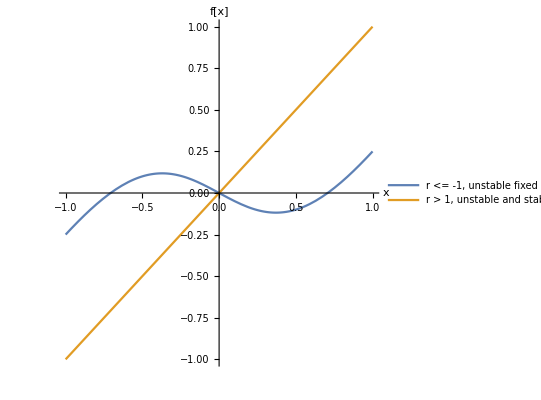
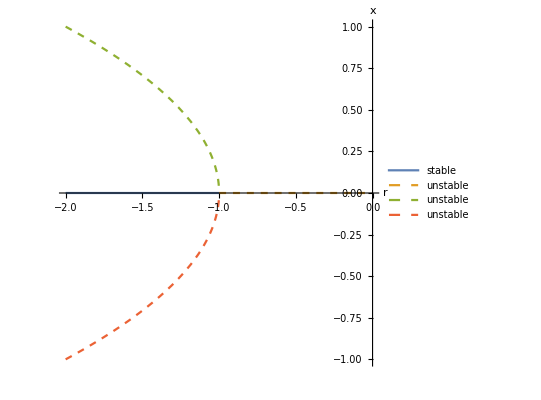

```mathematica
f[r_]:=x+r*x/(x^2+1);
{Plot[{f[-1.5],f[0]},{x,-1,1},PlotLegends->Placed[{"r <= -1, unstable fixed point", "r > 1, unstable and stable and unstable fixed point"},Below],AxesLabel->{"x","f[x]"},AspectRatio->1],Plot[{Piecewise[{{0,r<=-1},{-Infinity,r>-1}}],Piecewise[{{-Infinity,r<=-1},{0,r>-1}}],√(-1-r),-√(-1-r)},{r,-2,0},AxesLabel->{"r","x"},PlotLegends->Placed[{"stable","unstable","unstable","unstable"},Below],AspectRatio->1,PlotStyle->{Thick, Dashed, Dashed, Dashed}]}
```

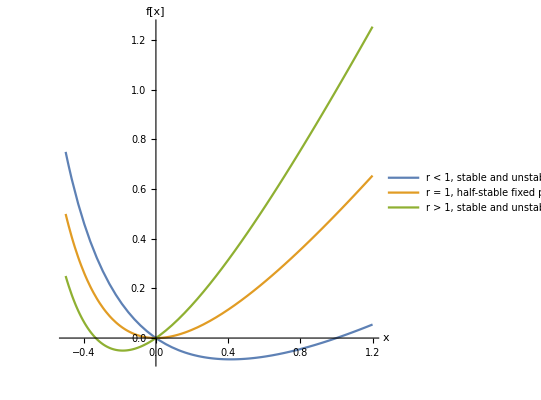
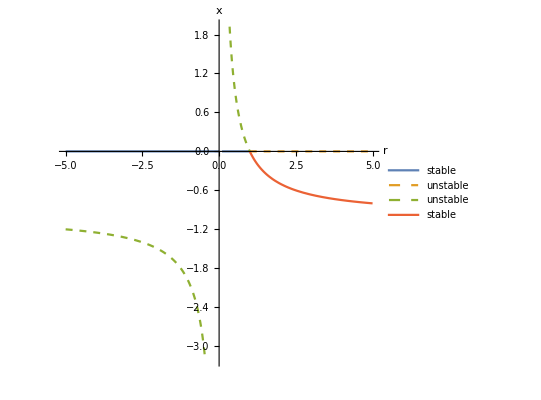

```mathematica
f[r_]:=r*x-x/(1+x);
{Plot[{f[0.5],f[1],f[1.5]},{x,-.5,1.2},PlotLegends->Placed[{"r < 1, stable and unstable fixed point","r = 1, half-stable fixed point", "r > 1, stable and unstable fixed point"},Below],AxesLabel->{"x","f[x]"},AspectRatio->1],Plot[{Piecewise[{{0,r<=1},{-Infinity,r>1}}],Piecewise[{{-Infinity,r<=1},{0,r>1}}],Piecewise[{{(1-r)/r,r≤1},{Infinity,r>1}}],Piecewise[{{Infinity,r≤1},{(1-r)/r,r>1}}]},{r,-5,5},Exclusions->r/(r-1)==0,AxesLabel->{r,x},PlotLegends->Placed[{"stable","unstable","unstable","stable"},Below],PlotStyle->{Thick,Dashed,Dashed,Thick},AspectRatio->1]}
```

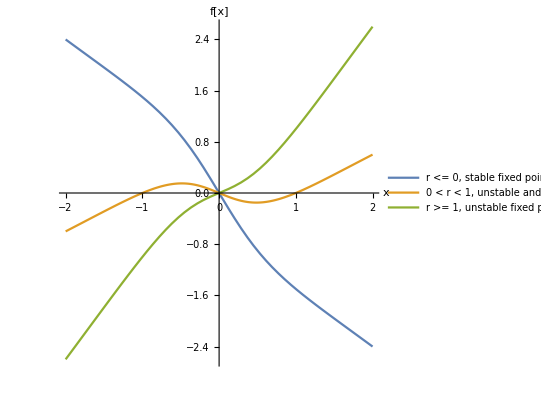
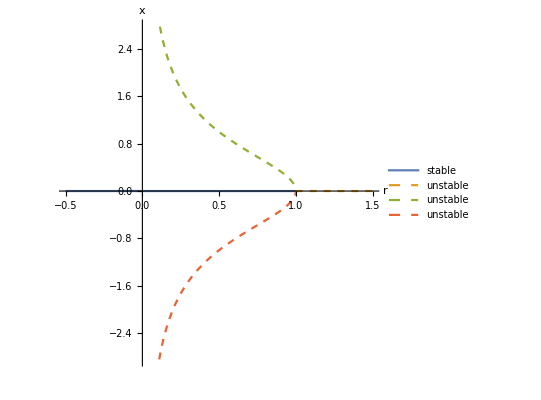

```mathematica
f[r_]:=r*x-x/(1+x^2);
{Plot[{f[-1],f[0.5],f[1.5]},{x,-2,2},AxesLabel->{"x","f[x]"},AspectRatio->1,PlotLegends->Placed[{"r <= 0, stable fixed point", "0 < r < 1, unstable and stable and unstable fixed points","r >= 1, unstable fixed point"},Below]], Plot[{Piecewise[{{0,r<=1},{-Infinity,r>1}}],Piecewise[{{-Infinity,r<=1},{0,r>1}}],(√(1-r))/(√r),-(√(1-r))/(√r)},{r,-0.5,1.5},AxesLabel->{r,x},PlotLegends->Placed[{"stable","unstable","unstable","unstable"},Below],PlotStyle->{Thick,Dashed,Dashed,Dashed},AspectRatio->1]}
```

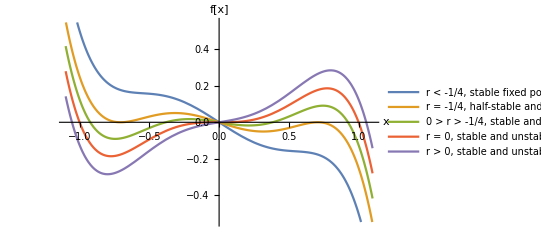
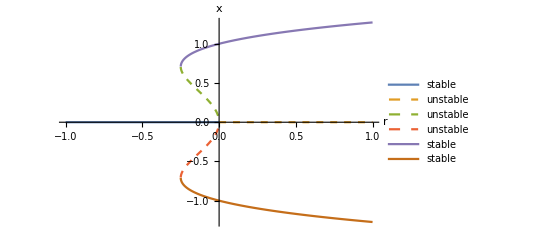

```mathematica
f[r_]:=r*x+x^3-x^5;
{Plot[{f[-1/2],f[-1/4],f[-1/8],f[0],f[1/8]},{x,-1.1,1.1},PlotLegends->Placed[{"r < -1/4, stable fixed point","r = -1/4, half-stable and stable and half-stable fixed points", "0 > r > -1/4, stable and unstable and stable and unstable and stable fixed points", "r = 0, stable and unstable and stable fixed points", "r > 0, stable and unstable and stable fixed points"},Below],PlotStyle->Thinning,AxesLabel->{"x","f[x]"}],Plot[{Piecewise[{{0,r≤0},{-Infinity,r>0}}],Piecewise[{{-Infinity,r≤0},{0,r>0}}],(√(1-√(1+4 r)))/(√2),-(√(1-√(1+4 r)))/(√2),(√(1+√(1+4 r)))/(√2),-(√(1+√(1+4 r)))/(√2)},{r,-1,1},AxesLabel->{r,x},PlotLegends->Placed[{"stable", "unstable", "unstable","unstable", "stable", "stable"},Below],PlotStyle->{Thick, Dashed, Dashed, Dashed, Thick, Thick}]}
```

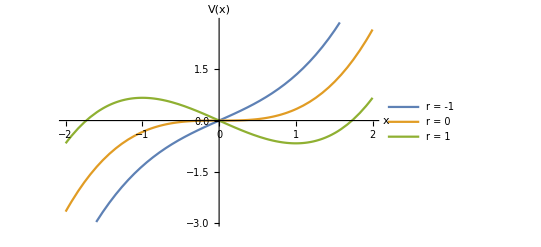

```mathematica
V[r_]:=x^3/3-r*x
Plot[{V[-1],V[0],V[1]},{x,-2,2},PlotLegends->{"r = -1", "r = 0", "r = 1"},AxesLabel->{"x","V(x)"}]
```

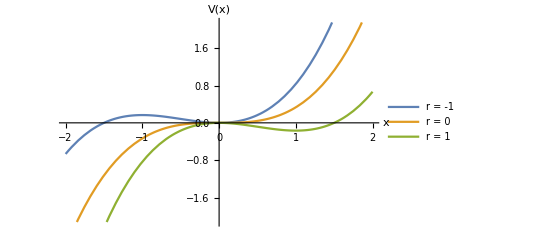

```mathematica
Plot[{x^3/3-(-1/2)x^2,x^3/3-(0/2)x^2,x^3/3-(1/2)x^2},{x,-2,2},PlotLegends->{"r = -1", "r = 0", "r = 1"},AxesLabel->{"x","V(x)"}]
```

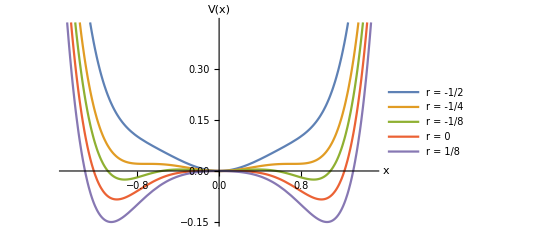

```mathematica
Plot[{1/6*x^6-1/4*x^4-(-1/2/2)x^2,1/6*x^6-1/4*x^4-(-1/4/2)x^2,1/6*x^6-1/4*x^4-(-1/8/2)x^2,1/6*x^6-1/4*x^4-(0/2)x^2,1/6*x^6-1/4*x^4-(1/8/2)x^2},{x,-1.5,1.5},PlotLegends->{"r = -1/2", "r = -1/4", "r = -1/8", "r = 0", "r = 1/8"},AxesLabel->{"x","V(x)"}]
```

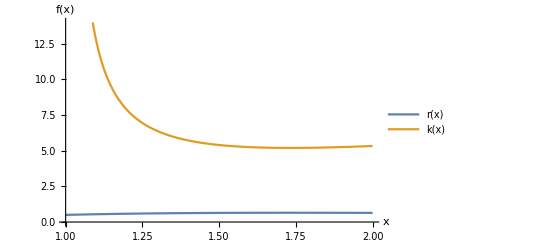

```mathematica
ClearAll[r,k,f];
r[x_]:=2 x^3/(1+x^2)^2;k[x_]:=2 x^3/(x^2-1);
Plot[{r[x],k[x]},{x,1,2},Exclusions->1/k[x]==0,PlotLegends->"Expressions",AxesLabel->{x,f[x]}]
```

```mathematica
{Limit[{r[x],k[x]},x->1],Limit[{r[x],k[x]},x->Infinity]}
```

{{1/2,∞},{0,∞}}

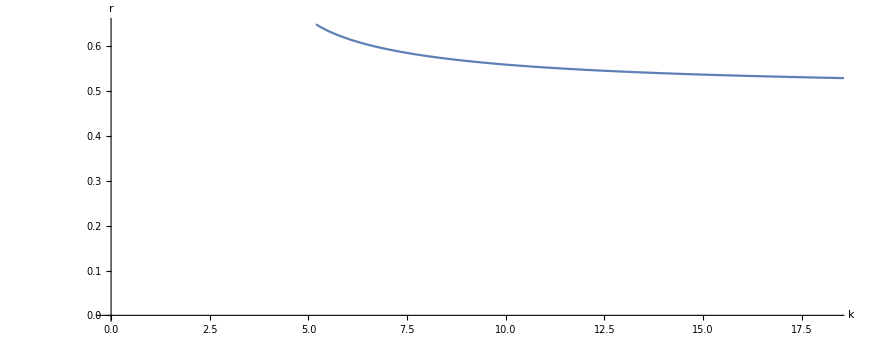

```mathematica
ParametricPlot[{k[x],r[x]},{x,1,√3},AxesLabel->{"k","r"},AxesOrigin->{0,0}]
```

```mathematica
Simplify[{D[r[x],x],D[k[x],x]}]
```

{-(2 x^2 (-3+x^2))/((1+x^2)^3),(2 x^2 (-3+x^2))/((-1+x^2)^2)}

```mathematica
{Solve[{D[r[x],x]==0},x],Solve[{D[k[x],x]==0},x]}
```

{{{x→0},{x→0},{x→-√3},{x→√3}},{{x→0},{x→0},{x→-√3},{x→√3}}}

```mathematica
{r[√3],k[√3]}
```

{(3 √3)/8,3 √3}

```mathematica
N[%]
```

{0.649519,5.19615}

```mathematica
Clear[x,h,a];
ContourPlot3D[{x(1-x)-h*x/(a+x)==0},{x,-5,5},{a,-5,5},{h,-5,5},AxesLabel->{x,a,h},MeshStyle->None]
```

-Graphics3D-

```mathematica
Solve[{x(1-x)==h*x/(a+x),1-2x==h*a/(x+a)^2},{h,a}]
```

{{h→(-1+x)^2,a→1-2 x}}

```mathematica
Solve[x(1-x)==h*x/(a+x),x]
```

{{x→0},{x→1/2 (1-a-√(1+2 a+a^2-4 h))},{x→1/2 (1-a+√(1+2 a+a^2-4 h))}}

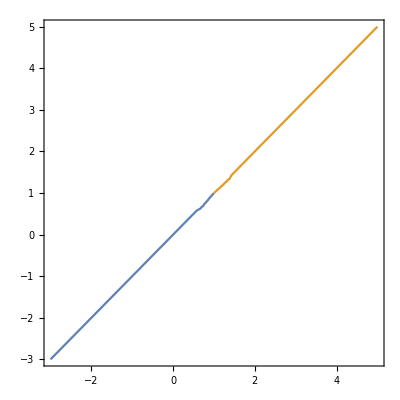

```mathematica
ContourPlot[{1/2 (1-a-√(1+2 a+a^2-4 h))==0,1/2 (1-a+√(1+2 a+a^2-4 h))==0},{a,-3,5},{h,-3,5}]
```

```mathematica
h[x_]:=(x-1)^2;a[x_]:=1-2x;{Limit[{h[x],a[x]},x->-Infinity],Limit[{h[x],a[x]},x->Infinity]}
```

{{∞,∞},{∞,-∞}}

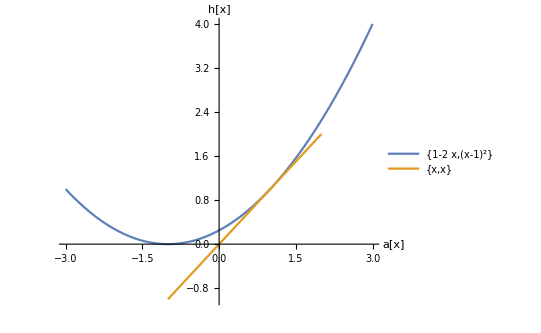

```mathematica
h[x_]:=(x-1)^2;a[x_]:=1-2x;
ParametricPlot[{{1-2x,(x-1)^2},{x,x}},{x,-1,2},PlotLegends->"Expressions",AxesLabel->{"a[x]","h[x]"}]
```

```mathematica
FullSimplify[D[x(1-x)-h*x/(a+x),x]]
```

1-2 x-(a h)/(a+x)^2

```mathematica
f[x_]:=1-2 x-(a h)/(a+x)^2
```

```mathematica
f[0]
```

1-h/a

```mathematica
f[(a-1)/2]
```

2-a-(a h)/(1/2 (-1+a)+a)^2

```mathematica
Solve[{2-a-(a h)/(1/2 (-1+a)+a)^2==0,a>0,h>0},{h}]
```

{{h→ConditionalExpression[-(-2+13 a-24 a^2+9 a^3)/(4 a),0<a<2]}}

```mathematica
FullSimplify[f[1/2 (1-a-√(1+2 a+a^2-4 h))]]
```

a+√((1+a)^2-4 h)-(4 a h)/((1+a-√((1+a)^2-4 h))^2)

```mathematica
Solve[{a+√((1+a)^2-4 h)-(4 a h)/((1+a-√((1+a)^2-4 h))^2)>=0,a>0,h>0},{h}]
```

{{h→ConditionalExpression[1/4 (1+2 a+a^2),a≥1]}}

```mathematica
FullSimplify[f[1/2 (1-a+√(1+2 a+a^2-4 h))]]
```

a-√((1+a)^2-4 h)-(4 a h)/((1+a+√((1+a)^2-4 h))^2)

```mathematica
Solve[{a-√((1+a)^2-4 h)-(4 a h)/((1+a+√((1+a)^2-4 h))^2)==0,a>0,h>0},{h}]
```

{{h→ConditionalExpression[a,a>1]},{h→ConditionalExpression[1/4 (1+2 a+a^2),0<a<1||a>1]}}